```mathematica
redBreasted2002=Import["C:\\Users\\katjad\\Desktop\\Random\\ebirdData\\eBirdDataGo\\red_breasted_2002.csv"];
redBreasted2003=Import["C:\\Users\\katjad\\Desktop\\Random\\ebirdData\\eBirdDataGo\\red_breasted_2003.csv"];redBreasted2004=Import["C:\\Users\\katjad\\Desktop\\Random\\ebirdData\\eBirdDataGo\\red_breasted_2004.csv"];redBreasted2005=Import["C:\\Users\\katjad\\Desktop\\Random\\ebirdData\\eBirdDataGo\\red_breasted_2005.csv"];redBreasted2006=Import["C:\\Users\\katjad\\Desktop\\Random\\ebirdData\\eBirdDataGo\\red_breasted_2006.csv"];redBreasted2007=Import["C:\\Users\\katjad\\Desktop\\Random\\ebirdData\\eBirdDataGo\\red_breasted_2007.csv"];redBreasted2008=Import["C:\\Users\\katjad\\Desktop\\Random\\ebirdData\\eBirdDataGo\\red_breasted_2008.csv"];redBreasted2009=Import["C:\\Users\\katjad\\Desktop\\Random\\ebirdData\\eBirdDataGo\\red_breasted_2009.csv"];
redBreasted2010=Import["C:\\Users\\katjad\\Desktop\\Random\\ebirdData\\eBirdDataGo\\red_breasted_2010.csv"];redBreasted2011=Import["C:\\Users\\katjad\\Desktop\\Random\\ebirdData\\eBirdDataGo\\red_breasted_2011.csv"];redBreasted2012=Import["C:\\Users\\katjad\\Desktop\\Random\\ebirdData\\eBirdDataGo\\red_breasted_2012.csv"];redBreasted2013=Import["C:\\Users\\katjad\\Desktop\\Random\\ebirdData\\eBirdDataGo\\red_breasted_2013.csv"];redBreasted2014=Import["C:\\Users\\katjad\\Desktop\\Random\\ebirdData\\eBirdDataGo\\red_breasted_2014.csv"];redBreasted2015=Import["C:\\Users\\katjad\\Desktop\\Random\\ebirdData\\eBirdDataGo\\red_breasted_2015.csv"];
```

Import the data (example for one year)

```mathematica
redBreasted2016=Import["C:\\Users\\katjad\\Desktop\\Random\\ebirdData\\eBirdDataGo\\red_breasted_2016.csv"];
```

Combine all the datasets in a list:

```mathematica
redBreastedLists={redBreasted2002,redBreasted2003,redBreasted2004,redBreasted2005,redBreasted2006,redBreasted2007,redBreasted2008,redBreasted2009,redBreasted2010,redBreasted2011,redBreasted2012,redBreasted2013,redBreasted2014,redBreasted2015,redBreasted2016};
```

Turn the lists into a list of associations each having a geographic position going to a list of values:

```mathematica
ratioAssociationList=Association[GeoPosition[{#[[1]],#[[2]]}]->{ #[[3]],#[[4]]}&/@#]&/@redBreastedLists;
```

Turn the Association into a list of ratios representing the fraction of checklists with species presence

```mathematica
ratioAssociation=Map[N[#[[2]]/#[[1]]]&,Merge[ratioAssociationList,Total]]
```

<|GeoPosition[{-39.,-59.}]→0.,GeoPosition[{50.,-94.}]→0.193548,GeoPosition[{26.,-83.}]→0.,GeoPosition[{46.,-56.}]→0.,GeoPosition[{-33.,-71.}]→0.,5559,GeoPosition[{-24.,-61.}]→0.,GeoPosition[{2.,-51.}]→0.,GeoPosition[{-23.,-56.}]→0.,GeoPosition[{-3.,-58.}]→0.|>
 |  |  |  |

```mathematica
GeoRegionValuePlot[ratioAssociation]
```

-Graphics-

```mathematica
GeoGraphics[KeyValueMap[{If[#2==0,LightOrange,Red],Rectangle[#1,GeoPosition[#1[[1]]+1]]}&,ratioAssociation],GeoBackground->"Satellite"]
```

-Graphics-

A custom color function to show the concentration of the birds over the area:

```mathematica
reds[n_]:=Blend[{Lighter[Orange,0.4],Red},n]
```

Plot the relative frequency of the bird sightings at each square:

```mathematica
GeoGraphics[KeyValueMap[{reds[#2*80],Rectangle[#1,GeoPosition[#1[[1]]+1]]}&,ratioAssociation]]
```

-Graphics-

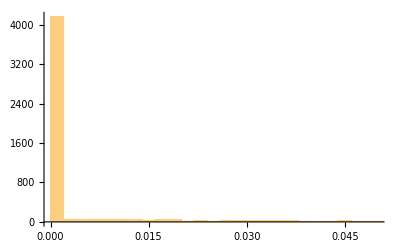

```mathematica
Histogram[ratioAssociation]
```

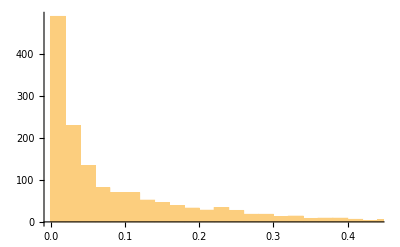

```mathematica
Histogram[Select[ratioAssociation,#>0&]]
```

```mathematica
FindDistribution[Select[Values[ratioAssociation],#>0&]]
```

ExtremeValueDistribution[0.0385314,0.0933907]